```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
EE[a_]=√(om 1/a^3+(1-om) F[a])
```

√(om/a^3+(1-om) F[a])

```mathematica
Ωm[a_]=om/(EE[a]^2 a^3)
```

om/(a^3 (om/a^3+(1-om) F[a]))

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
om=0.28;γ0=0.52;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {a,F[a]} = {0.5,1.86156×10^-8}.

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set1=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,-2.95019},{-0.045,-3.10931},{-0.04,-3.26843},{-0.035,-3.42755},{-0.03,-3.58668},{-0.025,-3.7458},{-0.02,-3.90492},{-0.015,-4.06404},{-0.01,-4.22316},{-0.005,-4.38228},{0.,-4.5414},{0.005,-4.70052},{0.01,-4.85964},{0.015,-5.01876},{0.02,-5.17788},{0.025,-5.337},{0.03,-5.49612},{0.035,-5.65524},{0.04,-5.81437},{0.045,-5.97349},{0.05,-6.13261}}

```mathematica
Y1=Interpolation[%]
```

InterpolatingFunction[…]

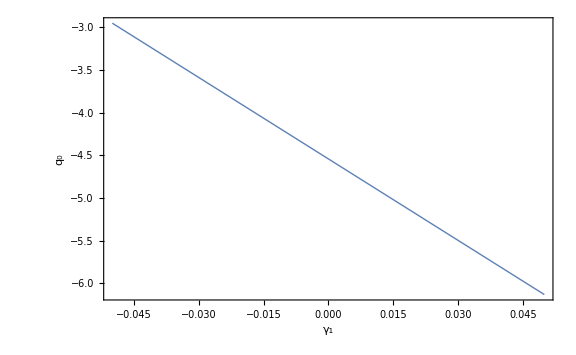

```mathematica
pl1=Plot[Y1[z],{z,-0.05,0.05},Frame->True,Axes->False,AxesLabel->{Style["γ_1", Black, FontSize->20], Style["q_0", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
γ0=0.59;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set3=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,0.399173},{-0.045,0.363813},{-0.04,0.328453},{-0.035,0.293093},{-0.03,0.257733},{-0.025,0.222373},{-0.02,0.187012},{-0.015,0.151652},{-0.01,0.116292},{-0.005,0.080932},{0.,0.0455718},{0.005,0.0102116},{0.01,-0.0251485},{0.015,-0.0605087},{0.02,-0.0958688},{0.025,-0.131229},{0.03,-0.166589},{0.035,-0.201949},{0.04,-0.237309},{0.045,-0.27267},{0.05,-0.30803}}

```mathematica
Y3=Interpolation[%]
```

InterpolatingFunction[…]

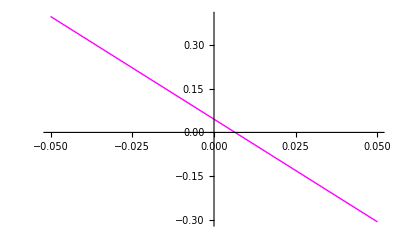

```mathematica
pl3=Plot[Y3[z],{z,-0.05,0.05},PlotStyle->{Thick,Magenta}]
```

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
γ0=0.55;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {a,F[a]} = {0.5,-1.02476×10^-9}.

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set2=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,-0.369849},{-0.045,-0.433497},{-0.04,-0.497145},{-0.035,-0.560794},{-0.03,-0.624442},{-0.025,-0.68809},{-0.02,-0.751738},{-0.015,-0.815387},{-0.01,-0.879035},{-0.005,-0.942683},{0.,-1.00633},{0.005,-1.06998},{0.01,-1.13363},{0.015,-1.19728},{0.02,-1.26092},{0.025,-1.32457},{0.03,-1.38822},{0.035,-1.45187},{0.04,-1.51552},{0.045,-1.57917},{0.05,-1.64281}}

```mathematica
Y2=Interpolation[%]
```

InterpolatingFunction[…]

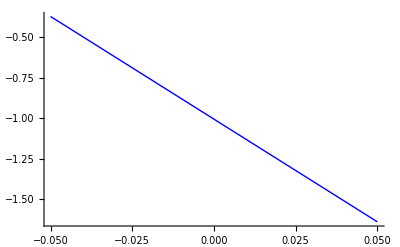

```mathematica
pl2=Plot[Y2[z],{z,-0.05,0.05},PlotStyle->{Thick,Blue}]
```

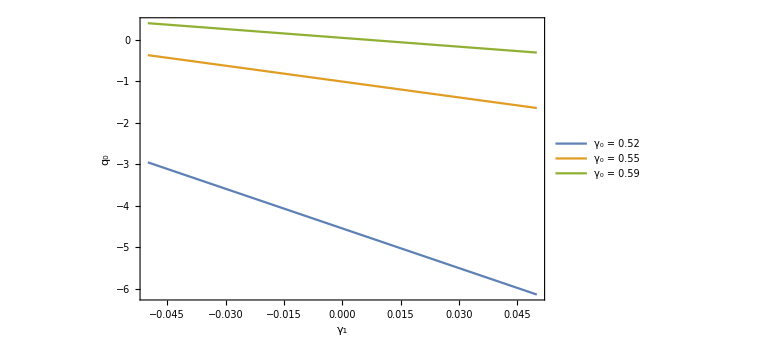

```mathematica
Plot[{Y1[z],Y2[z],Y3[z]},{z,-0.05,0.05},Frame->True,Axes->False,FrameLabel->{Style["γ_1",Black,14],Style["q_0",Black,15]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],ImageSize->Large,LabelStyle->{FontSize->10},PlotLegends->Placed[LineLegend[{
"γ_0 = 0.52","γ_0 = 0.55","γ_0 = 0.59"
},LabelStyle->{FontSize->10}],{0.8,0.4}]]
```

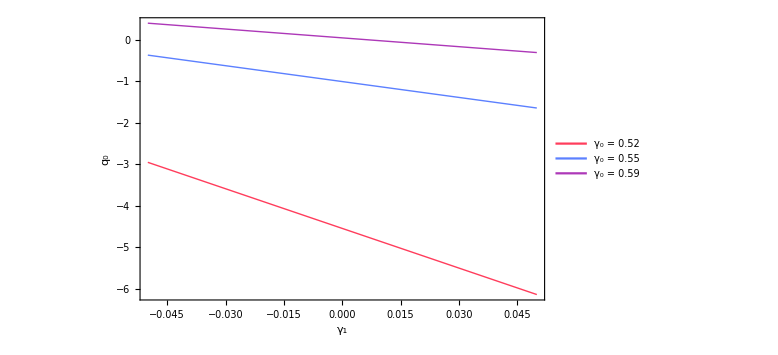

```mathematica
finalplot1=Plot[{Y1[z],Y2[z],Y3[z]},{z,-0.05,0.05},PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["γ_1", Black, FontSize->24, FontFamily->"Helvetica"],Style["q_0", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0 = 0.52","γ_0 = 0.55","γ_0 = 0.59"}, Background->White],{Left,Bottom}], Axes->False]
```

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
EE[a_]=√(om 1/a^3+(1-om) F[a])
```

√(0.28/a^3+0.72 F[a])

```mathematica
Ωm[a_]=om/(EE[a]^2 a^3)
```

0.28/(a^3 (0.28/a^3+0.72 F[a]))

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
om=0.3;γ0=0.52;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {a,F[a]} = {0.5,1.86156×10^-8}.

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set1=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,-2.85435},{-0.045,-3.00905},{-0.04,-3.16375},{-0.035,-3.31846},{-0.03,-3.47316},{-0.025,-3.62786},{-0.02,-3.78256},{-0.015,-3.93726},{-0.01,-4.09196},{-0.005,-4.24666},{0.,-4.40136},{0.005,-4.55606},{0.01,-4.71076},{0.015,-4.86546},{0.02,-5.02016},{0.025,-5.17486},{0.03,-5.32956},{0.035,-5.48427},{0.04,-5.63897},{0.045,-5.79367},{0.05,-5.94837}}

```mathematica
Y11=Interpolation[%]
```

InterpolatingFunction[…]

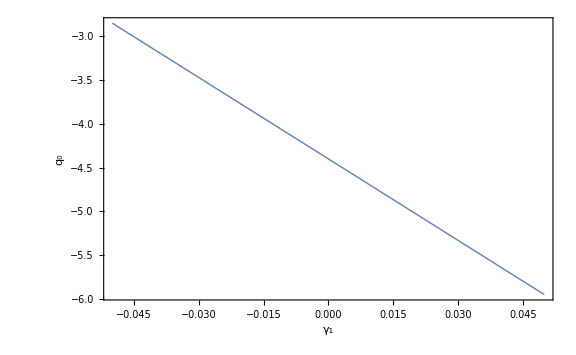

```mathematica
pl1=Plot[Y11[z],{z,-0.05,0.05},Frame->True,Axes->False,AxesLabel->{Style["γ_1", Black, FontSize->20], Style["q_0", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
γ0=0.59;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set3=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,0.401974},{-0.045,0.367596},{-0.04,0.333218},{-0.035,0.29884},{-0.03,0.264462},{-0.025,0.230084},{-0.02,0.195707},{-0.015,0.161329},{-0.01,0.126951},{-0.005,0.0925727},{0.,0.0581948},{0.005,0.0238169},{0.01,-0.0105611},{0.015,-0.044939},{0.02,-0.0793169},{0.025,-0.113695},{0.03,-0.148073},{0.035,-0.182451},{0.04,-0.216829},{0.045,-0.251207},{0.05,-0.285585}}

```mathematica
Y33=Interpolation[%]
```

InterpolatingFunction[…]

```mathematica
pl3=Plot[Y3[z],{z,-0.05,0.05},PlotStyle->{Thick,Magenta}]
```

-Graphics-

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
γ0=0.55;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {a,F[a]} = {0.5,-1.02476×10^-9}.

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set2=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,-0.345686},{-0.045,-0.407566},{-0.04,-0.469447},{-0.035,-0.531327},{-0.03,-0.593207},{-0.025,-0.655088},{-0.02,-0.716968},{-0.015,-0.778848},{-0.01,-0.840728},{-0.005,-0.902609},{0.,-0.964489},{0.005,-1.02637},{0.01,-1.08825},{0.015,-1.15013},{0.02,-1.21201},{0.025,-1.27389},{0.03,-1.33577},{0.035,-1.39765},{0.04,-1.45953},{0.045,-1.52141},{0.05,-1.58329}}

```mathematica
Y22=Interpolation[%]
```

InterpolatingFunction[…]

```mathematica
pl2=Plot[Y2[z],{z,-0.05,0.05},PlotStyle->{Thick,Blue}]
```

-Graphics-

```mathematica
Plot[{Y1[z],Y2[z],Y3[z]},{z,-0.05,0.05},Frame->True,Axes->False,FrameLabel->{Style["γ_1",Black,14],Style["q_0",Black,15]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],ImageSize->Large,LabelStyle->{FontSize->10},PlotLegends->Placed[LineLegend[{
"γ_0 = 0.52","γ_0 = 0.55","γ_0 = 0.59"
},LabelStyle->{FontSize->10}],{0.8,0.4}]]
```

-Graphics-

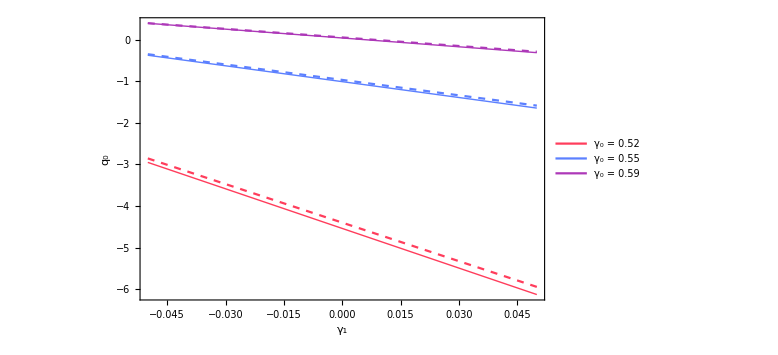

```mathematica
finalplot1=Plot[{Y1[z],Y2[z],Y3[z], Y11[z], Y22[z], Y33[z]},{z,-0.05,0.05},PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}, {Dashed, RGBColor[1,0.24,0.36]}, {Dashed, RGBColor[0.36,0.5,1]}, {Dashed, RGBColor[0.68,0.22,0.72]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["γ_1", Black, FontSize->24, FontFamily->"Helvetica"],Style["q_0", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0 = 0.52","γ_0 = 0.55","γ_0 = 0.59"}, Background->White],{Left,Bottom}], Axes->False]
```

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
EE[a_]=√(om 1/a^3+(1-om) F[a])
```

√(0.3/a^3+0.7 F[a])

```mathematica
Ωm[a_]=om/(EE[a]^2 a^3)
```

0.3/(a^3 (0.3/a^3+0.7 F[a]))

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
om=0.32;γ0=0.52;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {a,F[a]} = {0.5,-5.39464×10^-9}.

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set1=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,-2.72722},{-0.045,-2.87341},{-0.04,-3.01961},{-0.035,-3.16581},{-0.03,-3.312},{-0.025,-3.4582},{-0.02,-3.6044},{-0.015,-3.75059},{-0.01,-3.89679},{-0.005,-4.04299},{0.,-4.18918},{0.005,-4.33538},{0.01,-4.48158},{0.015,-4.62777},{0.02,-4.77397},{0.025,-4.92017},{0.03,-5.06636},{0.035,-5.21256},{0.04,-5.35876},{0.045,-5.50495},{0.05,-5.65115}}

```mathematica
Y111=Interpolation[%]
```

InterpolatingFunction[…]

```mathematica
pl1=Plot[Y11[z],{z,-0.05,0.05},Frame->True,Axes->False,AxesLabel->{Style["γ_1", Black, FontSize->20], Style["q_0", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

-Graphics-

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
γ0=0.59;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set3=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,0.415456},{-0.045,0.382968},{-0.04,0.350479},{-0.035,0.317991},{-0.03,0.285503},{-0.025,0.253015},{-0.02,0.220527},{-0.015,0.188039},{-0.01,0.155551},{-0.005,0.123062},{0.,0.0905743},{0.005,0.0580861},{0.01,0.0255979},{0.015,-0.00689021},{0.02,-0.0393784},{0.025,-0.0718665},{0.03,-0.104355},{0.035,-0.136843},{0.04,-0.169331},{0.045,-0.201819},{0.05,-0.234307}}

```mathematica
Y333=Interpolation[%]
```

InterpolatingFunction[…]

```mathematica
pl3=Plot[Y3[z],{z,-0.05,0.05},PlotStyle->{Thick,Magenta}]
```

-Graphics-

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
γ0=0.55;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {a,F[a]} = {0.5,-8.3288×10^-10}.

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set2=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,-0.305931},{-0.045,-0.36441},{-0.04,-0.422889},{-0.035,-0.481368},{-0.03,-0.539846},{-0.025,-0.598325},{-0.02,-0.656804},{-0.015,-0.715282},{-0.01,-0.773761},{-0.005,-0.83224},{0.,-0.890718},{0.005,-0.949197},{0.01,-1.00768},{0.015,-1.06615},{0.02,-1.12463},{0.025,-1.18311},{0.03,-1.24159},{0.035,-1.30007},{0.04,-1.35855},{0.045,-1.41703},{0.05,-1.47551}}

```mathematica
Y222=Interpolation[%]
```

InterpolatingFunction[…]

```mathematica
pl2=Plot[Y2[z],{z,-0.05,0.05},PlotStyle->{Thick,Blue}]
```

-Graphics-

```mathematica
Plot[{Y1[z],Y2[z],Y3[z]},{z,-0.05,0.05},Frame->True,Axes->False,FrameLabel->{Style["γ_1",Black,14],Style["q_0",Black,15]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],ImageSize->Large,LabelStyle->{FontSize->10},PlotLegends->Placed[LineLegend[{
"γ_0 = 0.52","γ_0 = 0.55","γ_0 = 0.59"
},LabelStyle->{FontSize->10}],{0.8,0.4}]]
```

-Graphics-

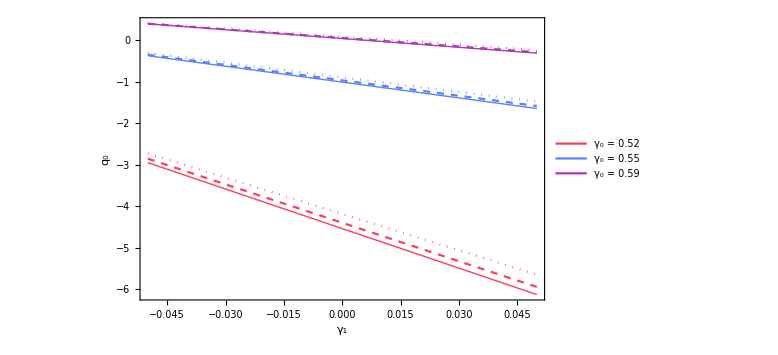

```mathematica
finalplot1=Plot[{Y1[z],Y2[z],Y3[z], Y11[z], Y22[z], Y33[z], Y111[z], Y222[z], Y333[z]},{z,-0.05,0.05},PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}, {Dashed, RGBColor[1,0.24,0.36]}, {Dashed, RGBColor[0.36,0.5,1]}, {Dashed, RGBColor[0.68,0.22,0.72]}, {Dotted, RGBColor[1,0.24,0.36]}, {Dotted, RGBColor[0.36,0.5,1]}, {Dotted, RGBColor[0.68,0.22,0.72]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["γ_1", Black, FontSize->24, FontFamily->"Helvetica"],Style["q_0", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0 = 0.52","γ_0 = 0.55","γ_0 = 0.59"}, Background->White],{Left,Bottom}], Axes->False]
```

```mathematica
SetDirectory["G:\\My Drive\\U\\paper"]
```

G:\My Drive\U\paper

```mathematica
(*Export["q_0VSgamma1.pdf",finalplot1,ImageResolution->500]*)
```

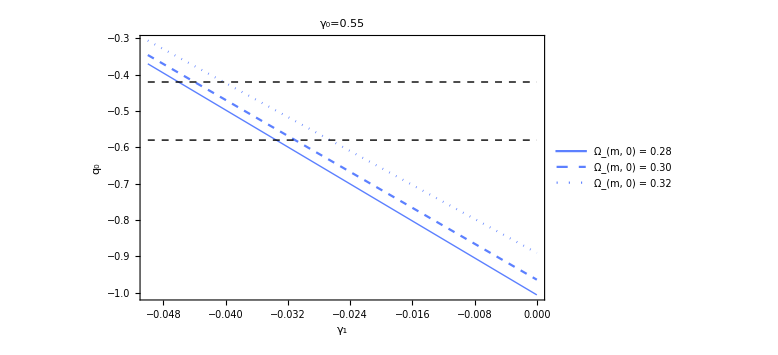

```mathematica
finalplot2=Plot[{Y2[z], Y22[z], Y222[z],-0.5+0.08,-0.5-0.08},{z,-0.05,0},PlotStyle->{{Thick, RGBColor[0.36,0.5,1]},{Dashed, RGBColor[0.36,0.5,1]},{Dotted, RGBColor[0.36,0.5,1]}, {Thick,Dashed, Black}, {Thick, Dashed, Black}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["γ_1", Black, FontSize->24, FontFamily->"Helvetica"],Style["q_0", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, Axes->False, PlotLabel->Style["γ_0=0.55", Black, FontSize->20],PlotLegends->Placed[LineLegend[{"Ω_(m, 0) = 0.28","Ω_(m, 0) = 0.30","Ω_(m, 0) = 0.32"}, Background->White],{Left,Bottom}]]
```

```mathematica
(*Export["q_0VSgamma1_bound.pdf",finalplot2,ImageResolution->500]*)
```

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
Clear[om]
om=0.28
```

0.28

```mathematica
EE[a_]=√(om 1/a^3+(1-om) F[a])
```

√(0.28/a^3+0.72 F[a])

```mathematica
Ωm[a_]=om/(EE[a]^2 a^3)
```

0.28/(a^3 (0.28/a^3+0.72 F[a]))

```mathematica
Clear[z]
```

```mathematica
FindRoot[Y2[z]==-0.5+0.08,{z,-0.041}]
```

{z→-0.0460603}

```mathematica
FindRoot[Y2[z]==-0.5-0.08,{z,-0.03}]
```

{z→-0.0334912}

```mathematica
(* View solution for one extreme *)
```

```mathematica
Clear[om]
```

```mathematica
om
```

om

```mathematica
om=0.28
```

0.28

```mathematica
γ0
```

0.55

```mathematica
Ωm[1]
```

0.28/(0.28+0.72 F[1])

```mathematica
γ1=-0.0460603;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

```mathematica
f[1]
```

0.49652 (1/(0.28+0.72 F[1]))^0.55

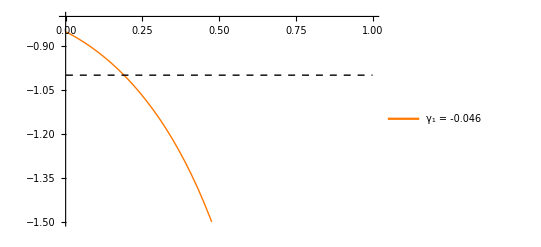

```mathematica
plw1=Plot[{w[z],-1},{z,0.001,1},PlotRange->{-1.5,-0.8},PlotStyle->{{Thick,RGBColor[1,0.47,0]},{Black,Dashed, Thick}}, PlotLegends->Placed[LineLegend[{"γ_1 = -0.046"}, Background->White],{Left,Bottom}],LabelStyle->{FontSize->14}]
```

```mathematica
(* Analytic expression: Fitting with polynomials *)
```

```mathematica
setF=Table[{z,Fz[z]},{z,0.01,1,0.01}];
```

```mathematica
P1=Fit[setF,{1,z},z]
```

1.2554-0.982046 z

```mathematica
w1[z_]=-1+(1+z) D[P1,z]/(3 P1)//Simplify
```

(1.61168-0.666667 z)/(-1.27835+1. z)

```mathematica
P2=Fit[setF,{1,z,z^2},z]
```

1.00563+0.487182 z-1.45468 z^2

```mathematica
w2[z_]=-1+(1+z) D[P2,z]/(3 P2)//Simplify
```

(0.579669+0.889937 z-0.333333 z^2)/(-0.691305-0.334906 z+1. z^2)

```mathematica
P3=Fit[setF,{1,z,z^2,z^3},z]
```

0.980774+0.775336 z-2.1644 z^2+0.468459 z^3

```mathematica
w3[z_]=-1+(1+z) D[P3,z]/(3 P3)//Simplify
```

(-1.54192-4.18355 z+2.54008 z^2-2.22045×10^-16 z^3)/(2.09362+1.65508 z-4.62025 z^2+1. z^3)

```mathematica
P4=Fit[setF,{1,z,z^2,z^3,z^4},z]
```

1.00488+0.318484 z-0.152465 z^2-2.61987 z^3+1.52887 z^4

```mathematica
w4[z_]=-1+(1+z) D[P4,z]/(3 P4)//Simplify
```

(-0.587828-0.205358 z-1.68035 z^2+1.33333 z^3+0.333333 z^4)/(0.657266+0.208313 z-0.0997238 z^2-1.71359 z^3+1. z^4)

```mathematica
Dif[z_]:=1-w5[z]/w[z]
```

```mathematica
Res=Table[{z,Dif[z]},{z,0.01,1.0,0.01}];
```

```mathematica
plotRes=ListPlot[Res]
```

-Graphics-

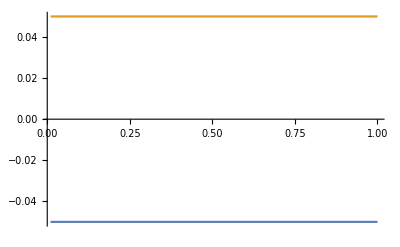

```mathematica
bounds=Plot[{-0.05,0.05},{x,0.01,1}]
```

```mathematica
Show[bounds,plotRes,PlotRange->All]
```

-Graphics-

```mathematica
P5=Fit[setF,{1,z,z^2,z^3,z^4,z^5},z]
```

0.998744+0.488757 z-1.30918 z^2+0.411054 z^3-1.83857 z^4+1.33364 z^5

```mathematica
w5[z_]=-1+(1+z) D[P5,z]/(3 P5)//Simplify
```

(-0.626725-0.898762 z+0.63544 z^2-1.83814 z^3+1.20713 z^4+0.666667 z^5)/(0.748886+0.366483 z-0.98166 z^2+0.30822 z^3-1.37861 z^4+1. z^5)

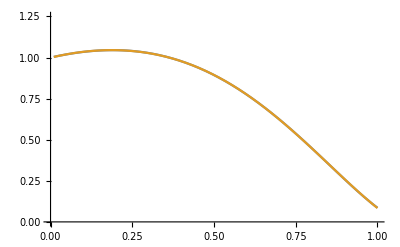

```mathematica
Plot[{Fz[z],P5},{z,0.01,1},PlotRange->{0,1.25}]
```

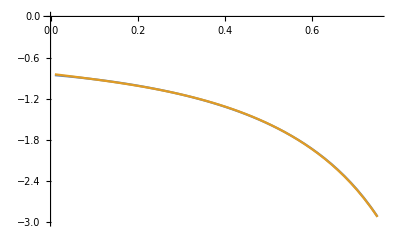

```mathematica
Plot[{w[z],w5[z]},{z,0.01,0.75},PlotRange->{-3,0}]
```

```mathematica
(* View solution for the other extreme *)
```

```mathematica
-0.03349120227773507
```

-0.0334912

```mathematica
γ1=-0.0334912;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

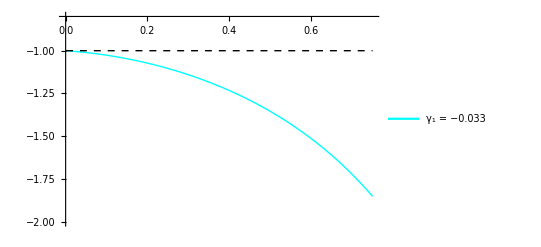

```mathematica
plw2=Plot[{w[z],-1},{z,0.001,0.75},PlotRange->{-2,-0.8},PlotStyle->{{Thick,Cyan},{Black,Dashed, Thick}}, PlotLegends->Placed[LineLegend[{"γ_1 = −0.033"}, Background->White],{Left,Bottom}], LabelStyle->{FontSize->14}]
```

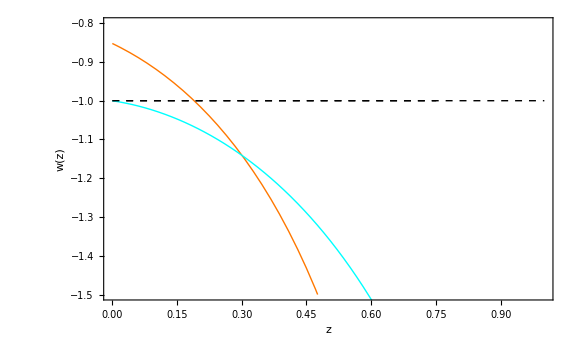

```mathematica
Show[plw1,plw2,PlotRange->{-1.5,-0.8},Frame->True,FrameLabel->{Style["z",Black,14],Style["w(z)",Black,15]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],Axes->False,ImageSize->Large]
```

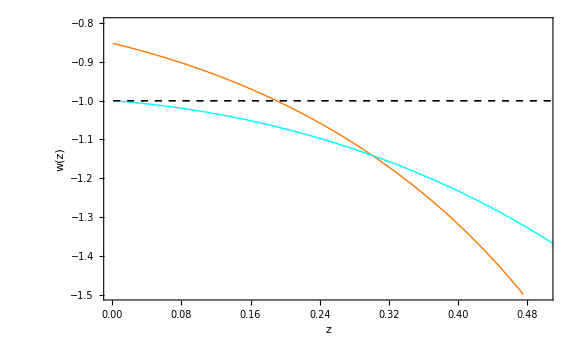

```mathematica
finalplot3=Show[plw1,plw2,PlotRange->{{0,0.5},{-1.5,-0.8}},ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24, FontFamily->"Helvetica"],Style["w(z)", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, Axes->False]
```

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
Clear[om]
```

```mathematica
om=0.3
```

0.3

```mathematica
EE[a_]=√(om 1/a^3+(1-om) F[a])
```

√(0.3/a^3+0.7 F[a])

```mathematica
Ωm[a_]=om/(EE[a]^2 a^3)
```

0.3/(a^3 (0.3/a^3+0.7 F[a]))

```mathematica
Clear[z]
```

```mathematica
FindRoot[Y22[z]==-0.5+0.08,{z,-0.041}]
```

{z→-0.0439954}

```mathematica
FindRoot[Y22[z]==-0.5-0.08,{z,-0.03}]
```

{z→-0.0310672}

```mathematica
(* View solution for one extreme *)
```

```mathematica
om=0.3
```

0.3

```mathematica
γ0
```

0.55

```mathematica
γ1=-0.0424945;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];ww[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

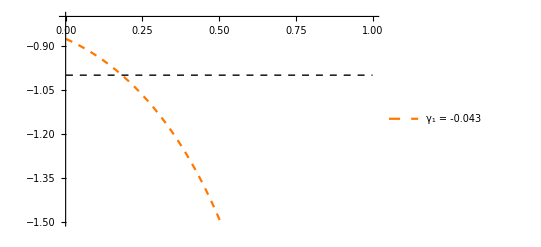

```mathematica
plw11=Plot[{ww[z],-1},{z,0.001,1},PlotRange->{-1.5,-0.8},PlotLegends->Placed[LineLegend[{"γ_1 = -0.043"}, Background->White],{Left,Bottom}],PlotStyle->{{Dashed,RGBColor[1,0.47,0]},{Black,Dashed, Thick}}, LabelStyle->{FontSize->14}]
```

```mathematica
(* Analytic expression: Fitting with polynomials *)
```

```mathematica
setF=Table[{z,Fz[z]},{z,0.01,1,0.01}];
```

```mathematica
P1=Fit[setF,{1,z},z]
```

1.22026-0.859156 z

```mathematica
w1[z_]=-1+(1+z) D[P1,z]/(3 P1)//Simplify
```

(1.75363-0.666667 z)/(-1.4203+1. z)

```mathematica
P2=Fit[setF,{1,z,z^2},z]
```

1.00286+0.41965 z-1.26614 z^2

```mathematica
w2[z_]=-1+(1+z) D[P2,z]/(3 P2)//Simplify
```

(0.681581+0.887626 z-0.333333 z^2)/(-0.792061-0.331439 z+1. z^2)

```mathematica
P3=Fit[setF,{1,z,z^2,z^3},z]
```

0.986425+0.61024 z-1.73556 z^2+0.309846 z^3

```mathematica
w3[z_]=-1+(1+z) D[P3,z]/(3 P3)//Simplify
```

(-2.5271-5.04724 z+2.86712 z^2)/(3.1836+1.96949 z-5.60137 z^2+1. z^3)

```mathematica
P4=Fit[setF,{1,z,z^2,z^3,z^4},z]
```

1.00254+0.304691 z-0.389954 z^2-1.75567 z^3+1.02253 z^4

```mathematica
w4[z_]=-1+(1+z) D[P4,z]/(3 P4)//Simplify
```

(-0.881128-0.452892 z-1.58986 z^2+1.33333 z^3+0.333333 z^4)/(0.980454+0.297977 z-0.381361 z^2-1.71698 z^3+1. z^4)

```mathematica
Dif[z_]:=1-w5[z]/w[z]
```

```mathematica
Res=Table[{z,Dif[z]},{z,0.01,1.0,0.01}];
```

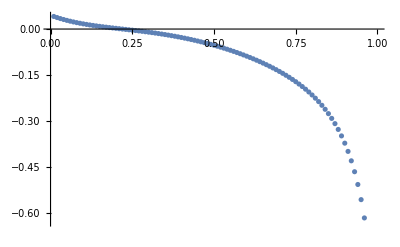

```mathematica
plotRes=ListPlot[Res]
```

```mathematica
bounds=Plot[{-0.05,0.05},{x,0.01,1}]
```

-Graphics-

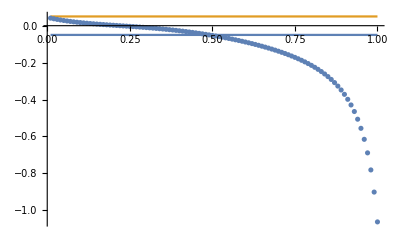

```mathematica
Show[bounds,plotRes,PlotRange->All]
```

```mathematica
P5=Fit[setF,{1,z,z^2,z^3,z^4,z^5},z]
```

0.999523+0.388601 z-0.959982 z^2-0.262034 z^3-0.63694 z^4+0.657216 z^5

```mathematica
w5[z_]=-1+(1+z) D[P5,z]/(3 P5)//Simplify
```

(-1.32375-1.36798 z+0.0881901 z^2-1.2922 z^3+1.34362 z^4+0.666667 z^5)/(1.52084+0.591283 z-1.46068 z^2-0.398703 z^3-0.969147 z^4+1. z^5)

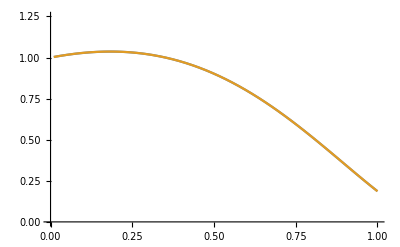

```mathematica
Plot[{Fz[z],P5},{z,0.01,1},PlotRange->{0,1.25}]
```

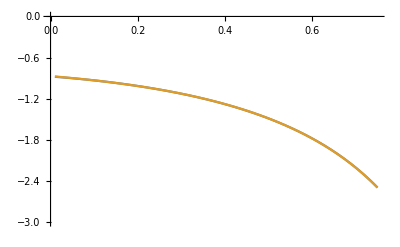

```mathematica
Plot[{w[z],w5[z]},{z,0.01,0.75},PlotRange->{-3,0}]
```

```mathematica
(* View solution for the other extreme *)
```

```mathematica
γ1=-0.0292051;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

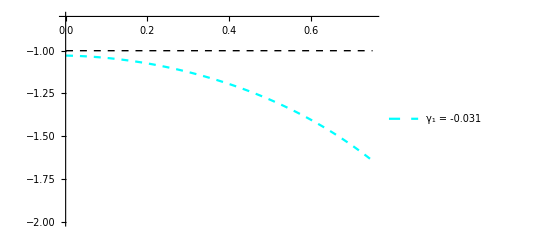

```mathematica
plw22=Plot[{w[z],-1},{z,0.001,0.75},PlotRange->{-2,-0.8},PlotStyle->{{Dashed,Cyan},{Black,Dashed, Thick}}, LabelStyle->{FontSize->14},PlotLegends->Placed[LineLegend[{"γ_1 = -0.031"}, Background->White],{Left,Bottom}]]
```

```mathematica
Show[plw1,plw2,PlotRange->{-1.5,-0.8},Frame->True,FrameLabel->{Style["z",Black,14],Style["w(z)",Black,15]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],Axes->False,ImageSize->Large]
```

-Graphics-

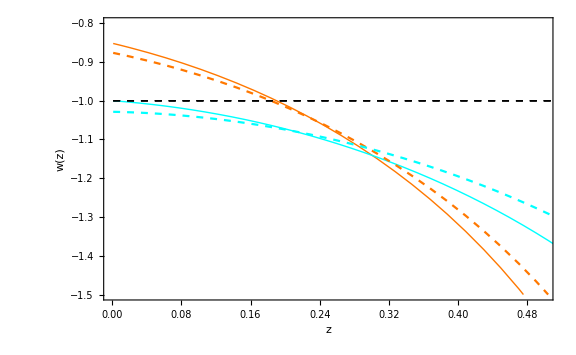

```mathematica
finalplot3=Show[plw1,plw2, plw11, plw22,PlotRange->{{0,0.5},{-1.5,-0.8}},ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24, FontFamily->"Helvetica"],Style["w(z)", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, Axes->False]
```

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
Clear[om]
```

```mathematica
om=0.32
```

0.32

```mathematica
EE[a_]=√(om 1/a^3+(1-om) F[a])
```

√(0.32/a^3+0.68 F[a])

```mathematica
Ωm[a_]=om/(EE[a]^2 a^3)
```

0.32/(a^3 (0.32/a^3+0.68 F[a]))

```mathematica
Clear[z]
```

```mathematica
FindRoot[Y222[z]==-0.5+0.08,{z,-0.041}]
```

{z→-0.040247}

```mathematica
FindRoot[Y222[z]==-0.5-0.08,{z,-0.03}]
```

{z→-0.0265668}

```mathematica
(* View solution for one extreme *)
```

```mathematica
om=0.32
```

0.32

```mathematica
γ0
```

0.55

```mathematica
γ1=-0.0424945;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];www[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

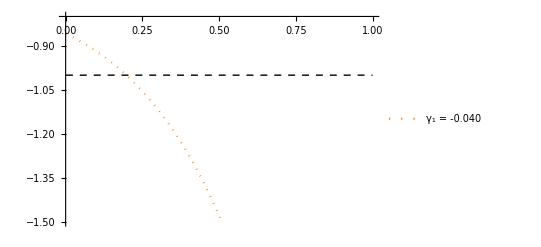

```mathematica
plw111=Plot[{www[z],-1},{z,0.001,1},PlotRange->{-1.5,-0.8},PlotStyle->{{Dotted,RGBColor[1,0.47,0]},{Black,Dashed, Thick}}, LabelStyle->{FontSize->14},PlotLegends->Placed[LineLegend[{"γ_1 = -0.040"}, Background->White],{Left,Bottom}]]
```

```mathematica
(* Analytic expression: Fitting with polynomials *)
```

```mathematica
setF=Table[{z,Fz[z]},{z,0.01,1,0.01}];
```

```mathematica
P1=Fit[setF,{1,z},z]
```

1.22877-0.856258 z

```mathematica
w1[z_]=-1+(1+z) D[P1,z]/(3 P1)//Simplify
```

(1.76837-0.666667 z)/(-1.43504+1. z)

```mathematica
P2=Fit[setF,{1,z,z^2},z]
```

1.00275+0.473224 z-1.31632 z^2

```mathematica
w2[z_]=-1+(1+z) D[P2,z]/(3 P2)//Simplify
```

(0.641951+0.906337 z-0.333333 z^2)/(-0.761786-0.359506 z+1. z^2)

```mathematica
P3=Fit[setF,{1,z,z^2,z^3},z]
```

0.986034+0.667066 z-1.79374 z^2+0.315132 z^3

```mathematica
w3[z_]=-1+(1+z) D[P3,z]/(3 P3)//Simplify
```

(-2.42336-5.20588 z+2.89735 z^2)/(3.12895+2.11678 z-5.69204 z^2+1. z^3)

```mathematica
P4=Fit[setF,{1,z,z^2,z^3,z^4},z]
```

1.00264+0.352364 z-0.407829 z^2-1.81225 z^3+1.05316 z^4

```mathematica
w4[z_]=-1+(1+z) D[P4,z]/(3 P4)//Simplify
```

(-0.8405-0.481213 z-1.59169 z^2+1.33333 z^3+0.333333 z^4)/(0.952026+0.334577 z-0.387242 z^2-1.72078 z^3+1. z^4)

```mathematica
Dif[z_]:=1-w5[z]/w[z]
```

```mathematica
Res=Table[{z,Dif[z]},{z,0.01,1.0,0.01}];
```

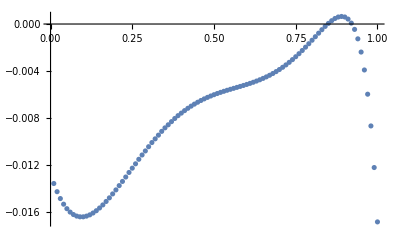

```mathematica
plotRes=ListPlot[Res]
```

```mathematica
bounds=Plot[{-0.05,0.05},{x,0.01,1}]
```

-Graphics-

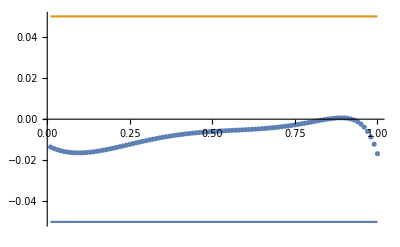

```mathematica
Show[bounds,plotRes,PlotRange->All]
```

```mathematica
P5=Fit[setF,{1,z,z^2,z^3,z^4,z^5},z]
```

0.999516+0.439029 z-0.996575 z^2-0.269576 z^3-0.6608 z^4+0.678797 z^5

```mathematica
w5[z_]=-1+(1+z) D[P5,z]/(3 P5)//Simplify
```

(-1.25689-1.40995 z+0.0922445 z^2-1.29798 z^3+1.34217 z^4+0.666667 z^5)/(1.47248+0.646776 z-1.46815 z^2-0.397138 z^3-0.973487 z^4+1. z^5)

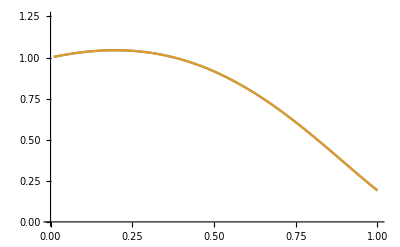

```mathematica
Plot[{Fz[z],P5},{z,0.01,1},PlotRange->{0,1.25}]
```

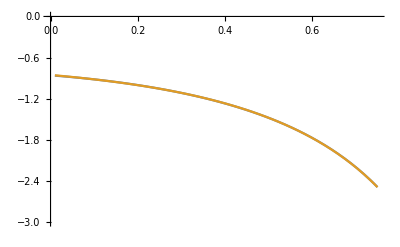

```mathematica
Plot[{w[z],w5[z]},{z,0.01,0.75},PlotRange->{-3,0}]
```

```mathematica
(* View solution for the other extreme *)
```

```mathematica
γ1=-0.0292051;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

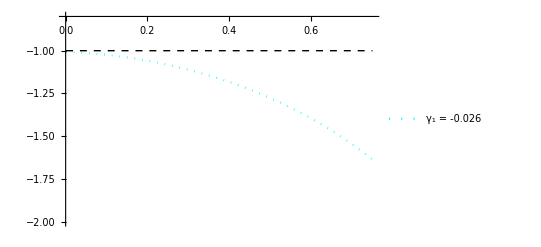

```mathematica
plw222=Plot[{w[z],-1},{z,0.001,0.75},PlotRange->{-2,-0.8},PlotStyle->{{Dotted,Cyan},{Black,Dashed, Thick}}, LabelStyle->{FontSize->14},PlotLegends->Placed[LineLegend[{"γ_1 = -0.026"}, Background->White],{Left,Bottom}]]
```

```mathematica
Show[plw1,plw2,PlotRange->{-1.5,-0.8},Frame->True,FrameLabel->{Style["z",Black,14],Style["w(z)",Black,15]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],Axes->False,ImageSize->Large]
```

-Graphics-

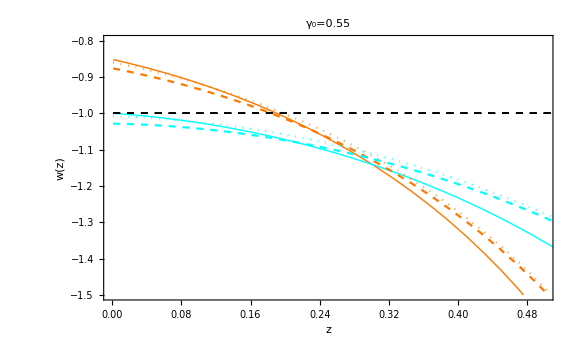

```mathematica
finalplot3=Show[plw1,plw2, plw11, plw22,plw111, plw222 ,PlotRange->{{0,0.5},{-1.5,-0.8}},ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24, FontFamily->"Helvetica"],Style["w(z)", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, Axes->False, PlotLabel->Style["γ_0=0.55", Black, FontSize->20]]
```

```mathematica
Export["wVSz_Extremes.pdf",finalplot3,ImageResolution->500]
```

wVSz_Extremes.pdf